# Linear Programming approach to Dynamic Programming

## Deterministic, fixed labor, utility defined globally

```mathematica
Clear[util,u,β,c]
```

Define utility function.
I use the exponential so that u[c] is defined everywhere, even for negative consumption.

```mathematica
u[c_]=-Exp[-10 c]
β=0.9;
```

-ⅇ^(-10 c)

```mathematica
u'[0]
```

10

### Concave production

Define production function.
I choose a quadratic because it is defined everywhere.
The steady state is 0.5

```mathematica
Clear[f]
f[k_]= 2k- k^2/2;
Solve[f'[k]==1/β,k][[1]];
kss=k/.%
```

0.888889

```mathematica
f'[kss]
```

1.11111

kvec will be the set of capital stocks. kvec begins with kmin + 1/numks  and ends with kmax. kmin and kmax should be chosen to so that (kmin, kmax) contains kss.

```mathematica
numks=5; kmin=0;kmax=1;
kvec=kmin+Range[numks]/numks//N;
```

We will formulate the problem so that tomorrow’s capital stock is the choice variable at each period.

Suppose the current state is kvec[[i]] and the choice is to choose kvec[[j]] for tomorrow’s capital stock. Then today’s consumption is

consumption = f[ kvec[[i]] ] - kvec[[j]]]

We define utility in terms of each period’s capital stock and the choice for gross investment. We do this for each pair of capital stocks:

```mathematica
Do[util[ik, jk]=u[f[kvec[[ik]]]-kvec[[jk]]],{ik,numks},{jk,numks}]
```

We now set up the optimization problem.

```mathematica
(* List the variables, V[i]*)
vars=Table[V[i],{i,numks}];
(* Form the objective, the sum of the V[i]'s *)
obj=Plus@@vars;
(* Define the constraint function that must hold if the current state is kvec[i] and gross investment is kvec[j] *)
constraint[i_,j_]:=V[i]-( util[i,j]+ β V[j])
(* Create a list of all the constraints *)
conss=Table[constraint[i,j]>= 0,{i,numks},{j,numks}]//Flatten;
Length[conss]
```

25

```mathematica
util[4,4]
```

-0.00822975

```mathematica
conss(*/.{V[1]->0,V[2]-> 0,V[3]-> 0,V[4]-> 0,V[5]-> 0}*)
```

{0.165299+0.1 V[1]≥0,1.2214+V[1]-0.9 V[2]≥0,9.02501+V[1]-0.9 V[3]≥0,66.6863+V[1]-0.9 V[4]≥0,492.749+V[1]-0.9 V[5]≥0,0.00551656-0.9 V[1]+V[2]≥0,0.0407622+0.1 V[2]≥0,0.301194+V[2]-0.9 V[3]≥0,2.22554+V[2]-0.9 V[4]≥0,16.4446+V[2]-0.9 V[5]≥0,0.000274654-0.9 V[1]+V[3]≥0,0.00202943-0.9 V[2]+V[3]≥0,0.0149956+0.1 V[3]≥0,0.110803+V[3]-0.9 V[4]≥0,0.818731+V[3]-0.9 V[5]≥0,0.0000203995-0.9 V[1]+V[4]≥0,0.000150733-0.9 V[2]+V[4]≥0,0.00111378-0.9 V[3]+V[4]≥0,0.00822975+0.1 V[4]≥0,0.0608101+V[4]-0.9 V[5]≥0,2.26033×10^-6-0.9 V[1]+V[5]≥0,0.0000167017-0.9 V[2]+V[5]≥0,0.00012341-0.9 V[3]+V[5]≥0,0.000911882-0.9 V[4]+V[5]≥0,0.00673795+0.1 V[5]≥0}

We now solve for the minimum of obj such that the constraints all hold.
For this we used the basic constrained optimization command in Mathematica because it is easy to formulate the problem this way.
Using Mathematica’s LinearProgramming command will surely be better.

```mathematica
sols=FindMinimum[{obj,conss},vars,AccuracyGoal->10];//AbsoluteTiming
```

{0.0474721,Null}

Notice the speed relative to the number of constraints.
We next collect the V[i] solutions and plot them

```mathematica
sols
```

{-2.29552,{V[1]→-1.58826,V[2]→-0.407622,V[3]→-0.149956,V[4]→-0.0822975,V[5]→-0.0673795}}

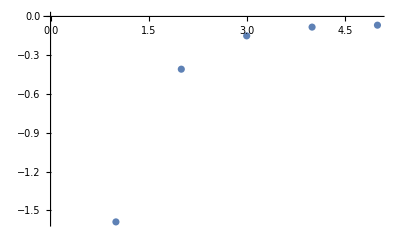

```mathematica
solV=sols[[2]];
vars/.solV;
ListPlot[%]
```

solV is a list of substitution rules. We use Dispatch to create an efficient representation of the rules:

```mathematica
?Dispatch
```

```mathematica
dispatch=Dispatch[solV]
```

Dispatch[…]

We want to find the policy. We need to evaluate the constraint[i, j] values at the solution and use the results to find the policy:

```mathematica
consss=
Table[
Table[constraint[i,j]/. dispatch,{j,numks}],
{i,numks}];//AbsoluteTiming
```

{0.0004377,Null}

```mathematica
consss=
Table[
Table[constraint[i,j],{j,numks}],
{i,numks}]/. dispatch;//AbsoluteTiming
```

{0.0005463,Null}

This shows the advantage of using Dispatch:

consss =
   Table[
     Table[constraint[i, j], {j, Length[kvec]}],
     {i, Length[kvec]}] /. solV; // AbsoluteTiming

{24.1894, Null}

The following constructs a two-column table policy, where policy[[i]] lists i and the j that lists the optimal choice for investment

```mathematica
policy=Table[{nk,Ordering[-consss[[nk]],-1][[1]]},{nk,1,numks}];
```

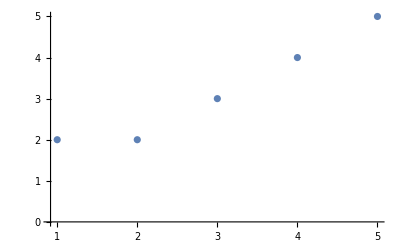

```mathematica
ListPlot[%]
```

We define the savings function

```mathematica
sav[i_]:=policy[[i,2]]
```

```mathematica
Table[sav[i]-i,{i,1,numks}]
```

{1,0,0,0,0}

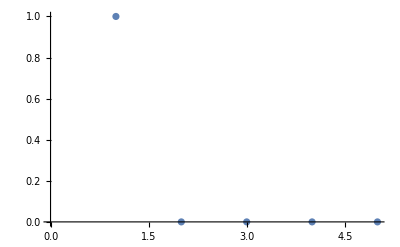

```mathematica
ListPlot[%]
```